```mathematica
P[x_,t_,p_]:=Piecewise[{{(1-p)^t Binomial[t,(t+x)/2](p/(1-p))^((t+x)/2),Mod[x,2]==0},{0,Mod[x,2]==1}}]
P1[x_,t_,p_]:=Sum[Binomial[t,m] p^m(1-p)^(t-m)KroneckerDelta[2m,t+x],{m,0,t}]
P2[x_,t_,p_]:=Piecewise[{{1/(√(2π t))(1-p)^t(p/(1-p))^((t+x)/2)2^(t+1)Exp[-x^2/(2 t)],Mod[x,2]==0},{0,Mod[x,2]==1}}]
P3[x_,t_,p_]:=Piecewise[{{2/(√(2π t))Exp[(-(x-(2p-1)t)^2)/(2 t)],Mod[x,2]==0},{0,Mod[x,2]==1}}]
```

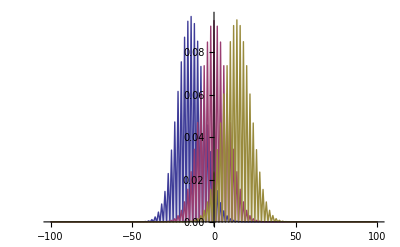

```mathematica
DiscretePlot[{P[x,70,0.4],P1[x,70,0.5],P3[x,70,0.6]},{x,-100,100},PlotRange->All]
```

```mathematica
S[n_]:=n^n Exp[-n] √(2π n)
```

```mathematica
Sum[P[x,10,0.7],{x,-10,10}]//N
```

1.

```mathematica
Mod[3,2]
```

1

```mathematica
(1-p)^t S[t]/(S[(t+x)/2]S[(t-x)/2])(p/(1-p))^((t+x)/2)//FullSimplify
```

(2^(1/2+t) (1-p)^t (p/(1-p))^((t+x)/2) t^(1/2+t) (t-x)^(1/2 (-1-t+x)) (t+x)^(1/2 (-1-t-x)))/(√π)

```mathematica
FullSimplify[(1-p)^t(p/(1-p))^((t+x)/2)2^(t+1)/.p->u+1/2]
```

2 (1-2 u)^t ((1+2 u)/(1-2 u))^((t+x)/2)

```mathematica
[2 (1-2 u)^t ((1+2 u)/(1-2 u))^((t+x)/2),u->0]
```

2